Andrea Halenkamp
Homework 5.1: #1,3

#### 1. x’=-0.06x+0.025y+0.2 y’=0.06x-0.075y

```mathematica
solutions1 = ParametricNDSolve[{x'[t]==-0.06x[t]+0.025y[t]+0.2,y'[t]==0.06x[t]-0.075y[t],x[0]==a,y[0]==b},{x,y},{t,20},{a,b}]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>]}

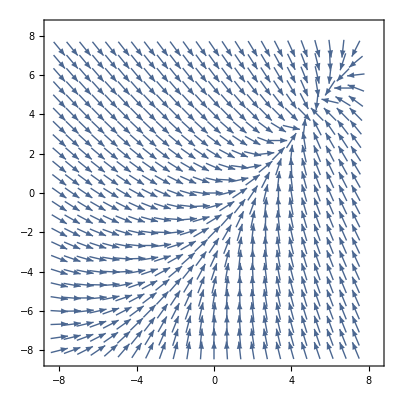

```mathematica
vectorplot1=VectorPlot[{-0.06x+0.025y+0.2,0.06x-0.075y},{x,-8,8},{y,-8,8},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine]
```

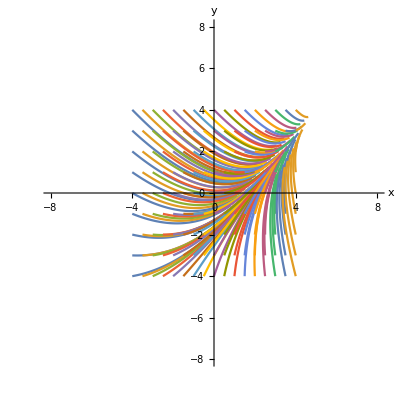

```mathematica
plot1=ParametricPlot[Evaluate[Table[{x[j,k][t], y[j,k][t]}/.solutions1,{j,-4,4,.5},{k,-4,4,1}]],{t,0,20},PlotRange->{{-8,8},{-8,8}},AxesLabel->{"x","y"}]
```

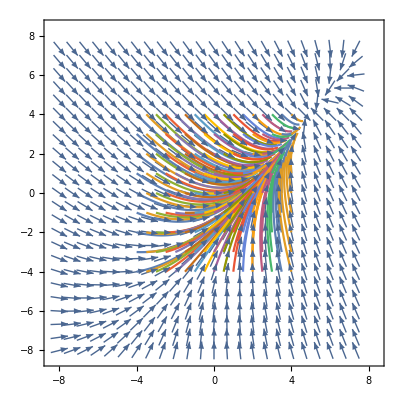

```mathematica
Show[vectorplot1,plot1]
```

#### 3. x’=x(2(1-x)-y) y’=y(-1/2+x)

```mathematica
solutions2 = ParametricNDSolve[{x'[t]==x[t](2(1-x[t])-y[t]),y'[t]==y[t](-1/2+x[t]),x[0]==a,y[0]==b},{x,y},{t,10},{a,b}]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>]}

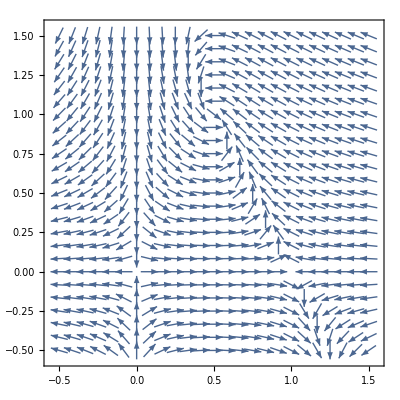

```mathematica
vectorplot2=VectorPlot[{x(2(1-x)-y),y(-1/2+x)},{x,-0.5,1.5},{y,-0.5,1.5},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine]
```

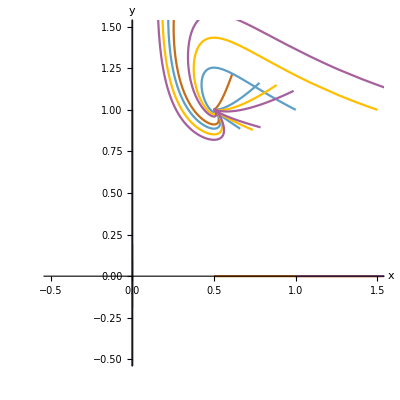

```mathematica
plot2=ParametricPlot[Evaluate[Table[{x[j,k][t], y[j,k][t]}/.solutions2,{j,-2,2,.5},{k,-2,2,1}]],{t,0,20},PlotRange->{{-0.5,1.5},{-0.5,1.5}},AxesLabel->{"x","y"}]
```

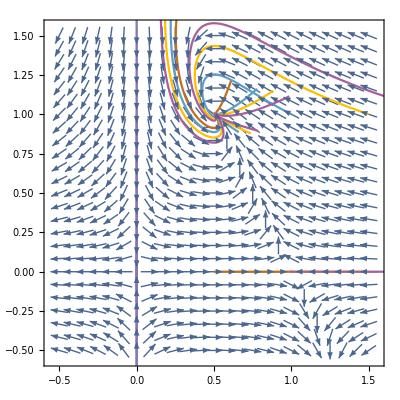

```mathematica
Show[vectorplot2,plot2]
```